```mathematica
quadsandtri=Table[allGraphs5[k,"colofour"],{k,alfa1s}]
```

{v13x24x5,v14x25x3,v1x24x35,v13x25x4,v14x2x35}

```mathematica
BaseCoeff3[formula_,base_]:=Table[Coefficient[formula,var],{var,Select[Bases[base,"Variables"],!MemberQ[quadsandtri,#]&]}]
```

```mathematica
matCrit=Sort[Map[BaseCoeff3[Total[ListofVars[#]],"C"]&,Select[ExpressionToList[allCrit],Intersection[ListofVars[#],Table[allGraphs5[k,"colofour"],{k,alfa1s}]]=={}&]]];
```

```mathematica
Select[Bases["C","Variables"],!MemberQ[quadsandtri,#]&][[8]]
```

v1x25x3x4

```mathematica
MatrixRank[matCrit]
```

0

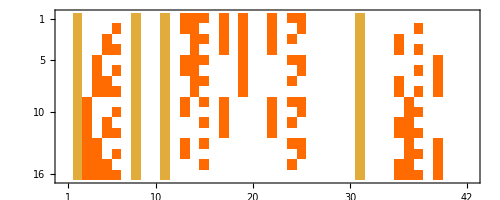

```mathematica
MatrixPlot[Take[matCrit,16]+Take[matCrit,-16]]
```

```mathematica
Total[matCrit]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Total[Transpose[matCrit]]
```

{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
MatrixPlot[matCrit, Mesh->All]
```

-Graphics-

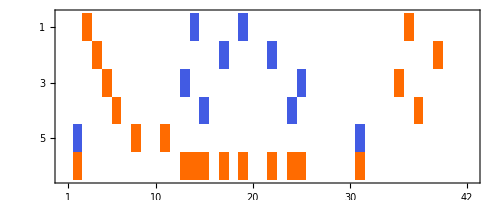

```mathematica
matCrit//LatticeReduce//MatrixPlot
```

```mathematica
ExpressionToList[allCrit]
```

{v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x24x5>0&&v13x25x4>0&&v14x235>0&&v14x25x3>0&&v14x2x35>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x24x35>0&&v1x2x34x5>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x24x5>0&&v13x25x4>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,541,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0}
 |  |  |  |

```mathematica
Select[ExpressionToList[allCrit],Intersection[ListofVars[#],Table[allGraphs5[k,"colofour"],{k,alfa1s}]]=={}&]
```

{v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x25>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x35>0&&v12x3x4x5>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x25>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x3x4>0&&v1x2x34x5>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x24>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x24>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x2x3x4>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x245>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0&&v1x2x3x45>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x235>0&&v14x2x3x5>0&&v15x24x3>0&&v1x23x4x5>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0,v124x3x5>0&&v12x35x4>0&&v134x2x5>0&&v135x2x4>0&&v13x2x45>0&&v13x2x4x5>0&&v14x23x5>0&&v14x2x3x5>0&&v15x24x3>0&&v1x235x4>0&&v1x245x3>0&&v1x24x3x5>0&&v1x25x34>0&&v1x25x3x4>0&&v1x2x35x4>0}